# Neighbourhood analyses including ICM composition scatter plots for the experimental data

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
fontOption="Arial";
```

```mathematica
colour3[i_]:=Join[{Darker[Gray]},(ColorData[16]/@{3,6,4})][[i]]
```

```mathematica
calcPlotRatioSortedByCellNumber[exprCell_,exprNeigh_,comp_,stages_,cellNumberPerEmbryo_,fateExcluded_:"TE"]:=Block[{cellPosPosNeighPropAll,numNeigh,cellNumbers,numPosCells,numNegCells,cellNegNegNeighPropAll,plotRatios},
cellPosPosNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprCell<>"+"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
cellNumbers=Table[Length[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&]],{i,1,Length[comp]}];
numPosCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]],{i,1,Length[comp]}];
numNegCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]],{i,1,Length[comp]}];
cellNegNegNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprNeigh<>"-"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
plotRatios=MapThread[Rule,{{"Stage","CellNumberEmbryo","CellNumberICM","NumPosCellsICM","NumNegCellsICM","MeanRatioNegNeighbNegCell","SEMRatioNegNeighbNegCell","MeanRatioPosNeighbPosCell","SEMRatioPosNeighbPosCell"},#}]&/@Table[{stages[[i]],cellNumberPerEmbryo[[i]],cellNumbers[[i]],numPosCells[[i]],numNegCells[[i]],Mean[cellNegNegNeighPropAll[[i]]],If[Length[cellNegNegNeighPropAll[[i]]]>1,(StandardDeviation[cellNegNegNeighPropAll[[i]]]/Sqrt[Length[cellNegNegNeighPropAll[[i]]]]),0],
Mean[cellPosPosNeighPropAll[[i]]],If[Length[cellPosPosNeighPropAll[[i]]]>1,(StandardDeviation[cellPosPosNeighPropAll[[i]]]/Sqrt[Length[cellPosPosNeighPropAll[[i]]]]),0]},{i,1,Length[cellNumbers]}];
SortBy[plotRatios,"CellNumber"/.#&]
]
```

```mathematica
calcPlotRatioAllCells[exprCell_,exprNeigh_,comp_,stages_,cellNumberPerEmbryo_,fateExcluded_:"TE"]:=Block[{cellPosPosNeighPropAll,numNeigh,cells,cellNumbers,cellNegNegNeighPropAll,plotRatios,numPosCells,numNegCells,centroids,distancesToCentroids},
cellPosPosNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprCell<>"+"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
cellNumbers=Table[Length[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&]],{i,1,Length[comp]}];
numPosCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]],{i,1,Length[comp]}];
numNegCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]],{i,1,Length[comp]}];
cellNegNegNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprNeigh<>"-"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
MapThread[Rule,{{"Stage","CellNumberEmbryo","CellNumberICM","NumPosCellsICM","NumNegCellsICM","RatiosNegNeighbNegCell","RatiosPosNeighbPosCell"},#}]&/@Table[{stages[[i]],cellNumberPerEmbryo[[i]],cellNumbers[[i]],numPosCells[[i]],numNegCells[[i]],cellNegNegNeighPropAll[[i]],cellPosPosNeighPropAll[[i]]},{i,1,Length[cellNumbers]}]
]
```

```mathematica
calcDistances[comp_,exprCell_]:=Block[{cells,centroids,maxDistanceToCentroid,distancesToCentroids,distancesPositive,distancesNegative},
cells=Table[Select[comp[[i,2,All,1]],#[[1]]≠"TE"&],{i,1,Length[comp]}];
centroids=Mean[#[[All,3]]]&/@cells;
distancesToCentroids=Table[EuclideanDistance[#,centroids[[i]]]&/@cells[[i,All,3]],{i,1,Length[cells]}];
maxDistanceToCentroid=Max/@distancesToCentroids;
distancesPositive=Table[Pick[distancesToCentroids[[i]],cells[[i,All,2]],z_/;StringContainsQ[z,exprCell<>"+"]],{i,1,Length[cells]}];
distancesNegative=Table[Pick[distancesToCentroids[[i]],cells[[i,All,2]],z_/;StringContainsQ[z,exprCell<>"-"]],{i,1,Length[cells]}];
Table[{"Stage"->comp[[i,1]],"maxDistanceToCentroid"->maxDistanceToCentroid[[i]],"distancesToCentroids"->distancesToCentroids[[i]],"distancesPositive"->distancesPositive[[i]],"distancesNegative"->distancesNegative[[i]]},{i,1,Length[comp]}]
]
```

```mathematica
calcDistNeighDistr[comp_, exprCell_]:=Block[{cells,centroid},
Table[cells=Select[comp[[j,2]],#[[1,1]]!="TE"&];
centroid=Mean[cells[[All,1,3]]];
{comp[[j,1]],Table[{"fate"->Switch[cells[[i,1,2]],z_/;StringContainsQ[z,exprCell<>"+"],"+",z_/;StringContainsQ[z,exprCell<>"-"],"-"],"distanceToCentroid"->EuclideanDistance[cells[[i,1,3]],centroid],"numNeighbours"->Length[cells[[i,2]]],"numPosNeighbours"->Length[Select[cells[[i,2]],StringContainsQ[#[[3]],"+"]&]],"numNegNeighbours"->Length[Select[cells[[i,2]],StringContainsQ[#[[3]],"-"]&]]},{i,1,Length[cells]}]},{j,1,Length[comp]}]
]
```

```mathematica
plotMeanStdLighter[xValues_,yValues_,smooth_,xLabel_,yLabel_,colour_]:=
Show[Table[ListLinePlot[{Transpose[{xValues[[i]],MeanFilter[#[[All,1]]+#[[All,2]],smooth]}],
Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]}&@yValues[[i]],PlotRange->{0,All},
PlotStyle->{Directive[Opacity[0.5],Lighter[colour[i],0.7]],Directive[Opacity[0.5],Lighter[colour[i],0.7]]},Filling->1->{2},FillingStyle->Directive[Opacity[0.5],Lighter[colour[i],0.5]],Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{xLabel,yLabel}],{i,1,Length[xValues]}],
ListLinePlot[Table[Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]],{i,1,Length[xValues]}],
PlotRange->{0,All},PlotStyle->Transpose[{ConstantArray[Thickness[0.007],Length[xValues]],Table[colour[i],{i,1,Length[xValues]}]}],Frame->{True,True,None,None},FrameStyle->Directive[Black,FontFamily->fontOption,14],FrameLabel->{xLabel,yLabel}]]
```

```mathematica
populationsColours={Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]};
```

## NANOG

### Importing data

#### SMD_2021_NG6G4

```mathematica
baseFolderSMD2021=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"SMD_2021_NG6G4")];
```

```mathematica
nanogNanogCompSMD2021=Import[FileNameJoin[{baseFolderSMD2021,"Results\\nanogNanogComp.mx"}]];
```

```mathematica
stagesSMD2021=nanogNanogCompSMD2021[[All,1,-1]];
```

```mathematica
numEmbryosSMD2021=Length[Select[stagesSMD2021,#>3.0&]]
```

116

```mathematica
cellNumberPerEmbryoSMD2021=Length/@nanogNanogCompSMD2021[[All,2]];
```

```mathematica
plotRatiosNSortedSMD2021=calcPlotRatioSortedByCellNumber["N","N",nanogNanogCompSMD2021,stagesSMD2021,cellNumberPerEmbryoSMD2021];
```

#### SMD_2020_NG6

```mathematica
baseFolderSMD2020=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"SMD_2020_NG6")];
```

```mathematica
nanogNanogCompSMD2020=Import[FileNameJoin[{baseFolderSMD2020,"Results\\nanogNanogComp.mx"}]];
```

```mathematica
stagesSMD2020=nanogNanogCompSMD2020[[All,1,3]];
```

```mathematica
numEmbryosSMD2020=Length[Select[stagesSMD2020,#>3.0&]]
```

44

```mathematica
cellNumberPerEmbryoSMD2020=Length/@nanogNanogCompSMD2020[[All,2]];
```

```mathematica
plotRatiosNSortedSMD2020=calcPlotRatioSortedByCellNumber["N","N",nanogNanogCompSMD2020,stagesSMD2020,cellNumberPerEmbryoSMD2020];
```

#### JLG_2021_NG6

```mathematica
baseFolderJLG2021=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<> "JLG_2021_NG6")];
```

```mathematica
nanogNanogCompJLG2021=Import[FileNameJoin[{baseFolderJLG2021,"Results\\nanogNanogComp.mx"}]];
```

```mathematica
stagesJLG2021=nanogNanogCompJLG2021[[All,1,3]];
```

```mathematica
numEmbryosJLG2021=Length[Select[stagesJLG2021,#>3.0&]]
```

132

```mathematica
cellNumberPerEmbryoJLG2021=Length/@nanogNanogCompJLG2021[[All,2]];
```

```mathematica
plotRatiosNSortedJLG2021=calcPlotRatioSortedByCellNumber["N","N",nanogNanogCompJLG2021,stagesJLG2021,cellNumberPerEmbryoJLG2021];
```

#### NS_ 2016_NG6

```mathematica
baseFolderNS2016=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"NS_2016_NG6")];
```

```mathematica
nanogNanogCompNS2016=Import[FileNameJoin[{baseFolderNS2016,"Results\\nanogNanogComp.mx"}]];
```

```mathematica
stagesNS2016=nanogNanogCompNS2016[[All,1,3]];
```

```mathematica
numEmbryosNS2016=Length[Select[stagesNS2016,#>3.0&]]
```

137

```mathematica
cellNumberPerEmbryoNS2016=Length/@nanogNanogCompNS2016[[All,2]];
```

```mathematica
plotRatiosNSortedNS2016=calcPlotRatioSortedByCellNumber["N","N",nanogNanogCompNS2016,stagesNS2016,cellNumberPerEmbryoNS2016];
```

#### NS_ 2020_NG6

```mathematica
baseFolderNS2020=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"NS_2020_NG6")];
```

```mathematica
nanogNanogCompNS2020=Import[FileNameJoin[{baseFolderNS2020,"Results\\nanogNanogComp.mx"}]];
```

```mathematica
stagesNS2020=nanogNanogCompNS2020[[All,1,3]];
```

```mathematica
numEmbryosNS2020=Length[Select[stagesNS2020,#>3.0&]]
```

189

```mathematica
cellNumberPerEmbryoNS2020=Length/@nanogNanogCompNS2020[[All,2]];
```

```mathematica
plotRatiosNSortedNS2020=calcPlotRatioSortedByCellNumber["N","N",nanogNanogCompNS2020,stagesNS2020,cellNumberPerEmbryoNS2020];
```

#### NS_2020_NRatG6Rb

```mathematica
baseFolderNS2020RatRb=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"NS_2020_NRatG6Rb")];
```

```mathematica
nanogNanogCompNS2020RatRb=Import[FileNameJoin[{baseFolderNS2020RatRb,"Results\\nanogNanogComp.mx"}]];
```

```mathematica
stagesNS2020RatRb=nanogNanogCompNS2020RatRb[[All,1,3]];
```

```mathematica
numEmbryosNS2020RatRb=Length[Select[stagesNS2020RatRb,#>3.0&]]
```

27

```mathematica
cellNumberPerEmbryoNS2020RatRb=Length/@nanogNanogCompNS2020RatRb[[All,2]];
```

```mathematica
plotRatiosNSortedNS2020RatRb=calcPlotRatioSortedByCellNumber["N","N",nanogNanogCompNS2020RatRb,stagesNS2020RatRb,cellNumberPerEmbryoNS2020RatRb];
```

#### NS_2020_NRatG6Gt

```mathematica
baseFolderNS2020RatGt=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"NS_2020_NRatG6Gt")];
```

```mathematica
nanogNanogCompNS2020RatGt=Import[FileNameJoin[{baseFolderNS2020RatGt,"Results\\nanogNanogComp.mx"}]];
```

```mathematica
stagesNS2020RatGt=nanogNanogCompNS2020RatGt[[All,1,3]];
```

```mathematica
numEmbryosNS2020RatGt=Length[Select[stagesNS2020RatGt,#>3.0&]]
```

76

```mathematica
cellNumberPerEmbryoNS2020RatGt=Length/@nanogNanogCompNS2020RatGt[[All,2]];
```

```mathematica
plotRatiosNSortedNS2020RatGt=calcPlotRatioSortedByCellNumber["N","N",nanogNanogCompNS2020RatGt,stagesNS2020RatGt,cellNumberPerEmbryoNS2020RatGt];
```

### ICM composition scatter plots

```mathematica
plotRatiosNSortedRaw=SortBy[#,"CellNumberICM"/.#&]&@Join[plotRatiosNSortedSMD2020,plotRatiosNSortedSMD2021,plotRatiosNSortedJLG2021,plotRatiosNSortedNS2016,plotRatiosNSortedNS2020,plotRatiosNSortedNS2020RatRb,plotRatiosNSortedNS2020RatGt];
```

```mathematica
plotRatiosNSorted=Select[plotRatiosNSortedRaw,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&&("Stage"/.#)>3.&];
```

```mathematica
Length[plotRatiosNSortedRaw]-Length[plotRatiosNSorted]
```

74

```mathematica
plotRatiosNSortedByStage=Table[Select[plotRatiosNSorted,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@plotRatiosNSortedByStage
```

{274,216,174}

```mathematica
correlByStageNm=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}]
```

{0.955877,0.958815,0.843674}

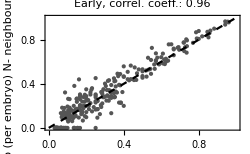
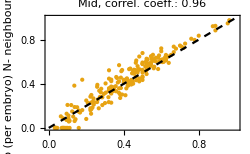
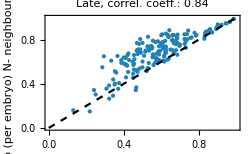

```mathematica
plotNeighbByStageNm=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion N- in ICM","mean ratio (per embryo)\nN- neighbours of N- cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageNm[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageNm.png"}],plotNeighbByStageNm]
```

```mathematica
correlByStageNp=Table [N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioPosNeighbPosCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}]
```

{0.975265,0.959432,0.757087}

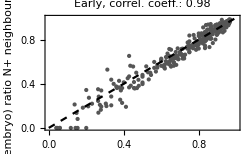
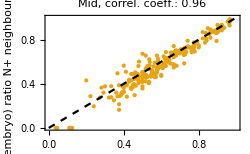
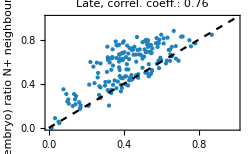

```mathematica
plotNeighbByStageNp=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion N+ in ICM","mean (per embryo) ratio\nN+ neighbours of N+ cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageNp[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageNp.png"}],plotNeighbByStageNp]
```

#### By experiment

```mathematica
plotRatiosNSortedRawByExp=SortBy[#,"CellNumberICM"/.#&]&/@{Join[plotRatiosNSortedSMD2021,plotRatiosNSortedJLG2021],plotRatiosNSortedSMD2020,plotRatiosNSortedNS2016,plotRatiosNSortedNS2020RatGt,plotRatiosNSortedNS2020RatRb,plotRatiosNSortedNS2020};
```

```mathematica
plotRatiosNSortedByExp=Table[Select[plotRatiosNSortedRawByExp[[i]],NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&&("Stage"/.#)>3.&],{i,1,Length[plotRatiosNSortedRawByExp]}];
```

```mathematica
Length[plotRatiosNSortedRawByExp]-Length[plotRatiosNSortedByExp]
```

0

```mathematica
plotRatiosNSortedByExpByStage=Table[Table[Select[plotRatiosNSortedByExp[[j]],("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}],{j,1,Length[plotRatiosNSortedByExp]}];
```

```mathematica
plotRatiosNSortedByExpByStage//Length
```

6

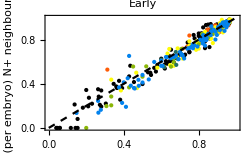
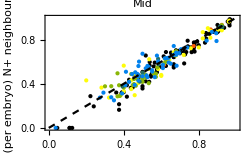
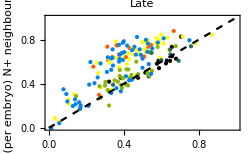

```mathematica
plotNeighbByExpByStageNp=Row[Table[Show[Graphics[Table[{ColorData[3][j],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosNSortedByExpByStage[[j,i]],{j,1,Length[plotRatiosNSortedByExpByStage]}],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion N+ in ICM","mean ratio (per embryo)\nN+ neighbours of N+ cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early","Mid","Late"}[[i]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByExpByStageNp.png"}],plotNeighbByExpByStageNp]
```

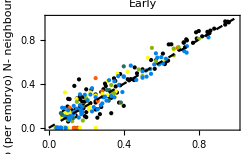
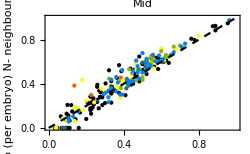
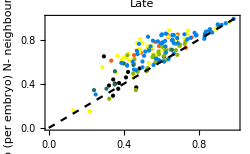

```mathematica
plotNeighbByExpByStageNm=Row[Table[Show[Graphics[Table[{ColorData[3][j],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosNSortedByExpByStage[[j,i]],{j,1,Length[plotRatiosNSortedByExpByStage]}],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion N- in ICM","mean ratio (per embryo)\nN- neighbours of N- cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early","Mid","Late"}[[i]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByExpByStageNm.png"}],plotNeighbByExpByStageNm]
```

```mathematica
neighbByExpLegend=SwatchLegend[ColorData[3]/@Range[Length[plotRatiosNSortedByExpByStage]],{"Data Set I","Data set II","Data Set III","Data set IV","Data set V","Data set VI"},LegendLayout->"Row"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByExpLegend.png"}],neighbByExpLegend]
```

### Population and neighbourhood distribution

```mathematica
nanogNanogComp=Join[nanogNanogCompSMD2020,nanogNanogCompSMD2021,nanogNanogCompJLG2021,nanogNanogCompNS2016,nanogNanogCompNS2020,nanogNanogCompNS2020RatRb,nanogNanogCompNS2020RatGt];
```

#### Plot populations

```mathematica
staging=nanogNanogComp[[All,1]];
```

```mathematica
popValues=#[[All,1;;2]]&/@nanogNanogComp[[All,2,All,1]];
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
popCountICM=Table[{populationsICM[[i,1]],{#,Count[populationsICM[[i,2,All,2]],#]}&/@{"N+G6+","N-G6-","N+G6-","N-G6+"}},{i,1, Length[populationsICM]}];
```

```mathematica
popCountICMByStage=Table[Select[popCountICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@popCountICMByStage
```

{326,218,177}

```mathematica
populationsByStageICM=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
popCountByStageICM=Table[{#,Count[Flatten[populationsByStageICM[[i,All,2]],1][[All,2]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,404},{N+G6+,3277},{N+G6-,1071},{N-G6+,1282}},{{N-G6-,134},{N+G6+,1191},{N+G6-,999},{N-G6+,1513}},{{N-G6-,862},{N+G6+,399},{N+G6-,2195},{N-G6+,3587}}}

```mathematica
popCountByStageICMTotal=Table[{#,Count[Flatten[populationsByStageICM[[i]][[All,2]]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,404},{N+G6+,3277},{N+G6-,1071},{N-G6+,1282}},{{N-G6-,134},{N+G6+,1191},{N+G6-,999},{N-G6+,1513}},{{N-G6-,862},{N+G6+,399},{N+G6-,2195},{N-G6+,3587}}}

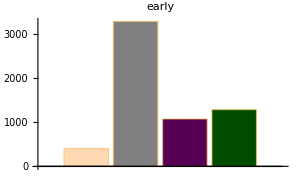
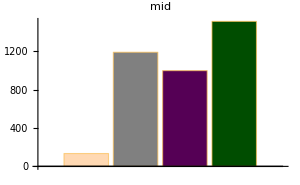
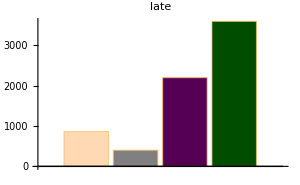

```mathematica
Labeled[Row[Table[BarChart[popCountByStageICMTotal[[i,All,2]],ImageSize->300,PlotLabel->Style[#,20,Black]&@({"early","mid","late"}[[i]]),ChartStyle->populationsColours,AxesStyle->Directive[Black,20]],{i,1,3}],"   "],SwatchLegend[populationsColours,{"DN","DP","Epi","PrE"}],Right]
```

#### Export absolute number of cells for each population to generate bar plot

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ResultsAll\\populationCountByStage.xlsx"}],{"early"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corrected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[1]]],
"mid"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corrected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[2]]],
"late"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corrected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[3]]]}]
```

#### Distribution population of neighbours

```mathematica
nanogNanogCompPop=nanogNanogComp/.{a_,"TE",_}->{a,"TE","TE"};
```

```mathematica
nanogNanogCompByStages={Select[nanogNanogCompPop,#[[1,3]]==3.5&],Select[nanogNanogCompPop,#[[1,3]]==4.0&],Select[nanogNanogCompPop,#[[1,3]]==4.5&]};
```

consider only ICM cells

```mathematica
nanogNanogCompByStagesICM=Table[{#[[1]],Select[#[[2]],#[[1,1]]!="TE"&]}&/@nanogNanogCompByStages[[i]],{i,1,3}];
```

```mathematica
propNeighboursOfPrEICM=Table[Table[{pop,If[Length[#]>0,N@Count[#[[All,-2]],pop]/Length[#],0]&/@Select[Flatten[nanogNanogCompByStagesICM[[i,All,2]],1],#[[1,2]]=="N-G6+"&][[All,2]]},{pop,{"TE","N-G6-","N+G6+","N+G6-","N-G6+"}}],{i,1,3}];
```

```mathematica
propNeighboursOfDPICM=Table[Table[{pop,If[Length[#]>0,N@Count[#[[All,-2]],pop]/Length[#],0]&/@Select[Flatten[nanogNanogCompByStagesICM[[i,All,2]],1],#[[1,2]]=="N+G6+"&][[All,2]]},{pop,{"TE","N-G6-","N+G6+","N+G6-","N-G6+"}}],{i,1,3}];
```

```mathematica
propNeighboursOfDNICM=Table[Table[{pop,If[Length[#]>0,N@Count[#[[All,-2]],pop]/Length[#],0]&/@Select[Flatten[nanogNanogCompByStagesICM[[i,All,2]],1],#[[1,2]]=="N-G6-"&][[All,2]]},{pop,{"TE","N-G6-","N+G6+","N+G6-","N-G6+"}}],{i,1,3}];
```

```mathematica
propNeighboursOfEpiICM=Table[Table[{pop,If[Length[#]>0,N@Count[#[[All,-2]],pop]/Length[#],0]&/@Select[Flatten[nanogNanogCompByStagesICM[[i,All,2]],1],#[[1,2]]=="N+G6-"&][[All,2]]},{pop,{"TE","N-G6-","N+G6+","N+G6-","N-G6+"}}],{i,1,3}];
```

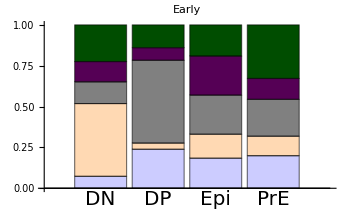
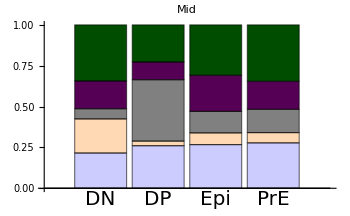
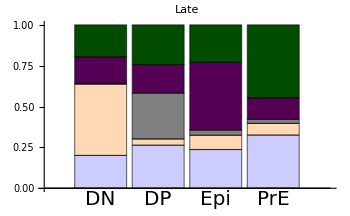

```mathematica
neighbourTypePopulationExpICM=Labeled[Row[Table[BarChart[{
Mean[#]&/@Transpose[Select[Transpose[propNeighboursOfDNICM[[i,All,2]]],Total[#]>0&]],
Mean[#]&/@Transpose[Select[Transpose[propNeighboursOfDPICM[[i,All,2]]],Total[#]>0&]],
Mean[#]&/@Transpose[Select[Transpose[propNeighboursOfEpiICM[[i,All,2]]],Total[#]>0&]],
Mean[#]&/@Transpose[Select[Transpose[propNeighboursOfPrEICM[[i,All,2]]],Total[#]>0&]]},ChartLayout->"Stacked",ChartStyle->{Lighter[Blue,0.8],Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},AxesStyle->Directive[Black,FontFamily->"Arial",20],ChartLabels->{Style[#,Black,FontFamily->"Arial",20]&/@{"DN","DP","Epi","PrE"},None},PlotLabel->(Style[#,Black,FontFamily->"Arial",20]&@(({"Early","Mid","Late"}[[i]]))),ImageSize->350],{i,1,3}]],SwatchLegend[{Lighter[Blue,0.8],Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},Style[#,Black,FontFamily->"Arial",20]&/@{"TE","DN","DP","Epi","PrE"},LegendLayout->"Row"]]
```

#### Export

```mathematica
exportList[stageIndex_]:={"DN cells"->Join[{{"Our embryo data: proportion of population of neighbours", "","","",DateString[]},{"ICM cells, Staging by cell number ","each row represents one cell"},{"TE","DN","DP","Epi","PrE"}},Transpose[propNeighboursOfDNICM[[stageIndex,All,2]]]],
"DP cells"->Join[{{"Our embryo data: proportion of population of neighbours", "","","",DateString[]},{"ICM cells, Staging by cell number ","each row represents one cell"},{"TE","DN","DP","Epi","PrE"}},Transpose[propNeighboursOfDPICM[[stageIndex,All,2]]]],
"EPI cells"->Join[{{"Our embryo data: proportion of population of neighbours", "","","",DateString[]},{"ICM cells, Staging by cell number ","each row represents one cell"},{"TE","DN","DP","Epi","PrE"}},Transpose[propNeighboursOfEpiICM[[stageIndex,All,2]]]],"PRE cells"->Join[{{"Our embryo data: proportion of population of neighbours", "","","",DateString[]},{"ICM cells, Staging by cell number ","each row represents one cell"},{"TE","DN","DP","Epi","PrE"}},Transpose[propNeighboursOfPrEICM[[stageIndex,All,2]]]]}
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ResultsAll\\neighDistrByStageICMfiveCatEarly.xlsx"}],exportList[1]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ResultsAll\\neighDistrByStageICMfiveCatMid.xlsx"}],exportList[2]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ResultsAll\\neighDistrByStageICMfiveCatLate.xlsx"}],exportList[3]]
```

## GATA6

### Importing data

#### SMD_2021_NG6G4

```mathematica
baseFolderSMD2021=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"SMD_2021_NG6G4")];
```

```mathematica
gata6Gata6CompSMD2021=Import[FileNameJoin[{baseFolderSMD2021,"Results\\gata6Gata6Comp.mx"}]];
```

```mathematica
stagesSMD2021=gata6Gata6CompSMD2021[[All,1,3]];
```

```mathematica
cellNumberPerEmbryoSMD2021=Length/@gata6Gata6CompSMD2021[[All,2]];
```

```mathematica
plotRatiosG6SortedSMD2021=calcPlotRatioSortedByCellNumber["G6","G6",gata6Gata6CompSMD2021,stagesSMD2021,cellNumberPerEmbryoSMD2021];
```

#### SMD_2020_NG6

```mathematica
baseFolderSMD2020=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"SMD_2020_NG6")];
```

```mathematica
gata6Gata6CompSMD2020=Import[FileNameJoin[{baseFolderSMD2020,"Results\\gata6Gata6Comp.mx"}]];
```

```mathematica
stagesSMD2020=gata6Gata6CompSMD2020[[All,1,3]];
```

```mathematica
cellNumberPerEmbryoSMD2020=Length/@gata6Gata6CompSMD2020[[All,2]];
```

```mathematica
plotRatiosG6SortedSMD2020=calcPlotRatioSortedByCellNumber["G6","G6",gata6Gata6CompSMD2020,stagesSMD2020,cellNumberPerEmbryoSMD2020];
```

#### JLG_2021_NG6

```mathematica
baseFolderJLG2021=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"JLG_2021_NG6")];
```

```mathematica
gata6Gata6CompJLG2021=Import[FileNameJoin[{baseFolderJLG2021,"Results\\gata6Gata6Comp.mx"}]];
```

```mathematica
stagesJLG2021=gata6Gata6CompJLG2021[[All,1,3]];
```

```mathematica
cellNumberPerEmbryoJLG2021=Length/@gata6Gata6CompJLG2021[[All,2]];
```

```mathematica
plotRatiosG6SortedJLG2021=calcPlotRatioSortedByCellNumber["G6","G6",gata6Gata6CompJLG2021,stagesJLG2021,cellNumberPerEmbryoJLG2021];
```

#### NS_2016_NG6

```mathematica
baseFolderNS2016=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"NS_2016_NG6")];
```

```mathematica
gata6Gata6CompNS2016=Import[FileNameJoin[{baseFolderNS2016,"Results\\gata6Gata6Comp.mx"}]];
```

```mathematica
stagesNS2016=gata6Gata6CompNS2016[[All,1,3]];
```

```mathematica
cellNumberPerEmbryoNS2016=Length/@gata6Gata6CompNS2016[[All,2]];
```

```mathematica
plotRatiosG6SortedNS2016=calcPlotRatioSortedByCellNumber["G6","G6",gata6Gata6CompNS2016,stagesNS2016,cellNumberPerEmbryoNS2016];
```

#### NS_2020_NG6

```mathematica
baseFolderNS2020=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"NS_2020_NG6")];
```

```mathematica
gata6Gata6CompNS2020=Import[FileNameJoin[{baseFolderNS2020,"Results\\gata6Gata6Comp.mx"}]];
```

```mathematica
stagesNS2020=gata6Gata6CompNS2020[[All,1,3]];
```

```mathematica
cellNumberPerEmbryoNS2020=Length/@gata6Gata6CompNS2020[[All,2]];
```

```mathematica
plotRatiosG6SortedNS2020=calcPlotRatioSortedByCellNumber["G6","G6",gata6Gata6CompNS2020,stagesNS2020,cellNumberPerEmbryoNS2020];
```

#### NS_2020_NRatG6Rb

```mathematica
baseFolderNS2020RatRb=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"NS_2020_NRatG6Rb")];
```

```mathematica
gata6Gata6CompNS2020RatRb=Import[FileNameJoin[{baseFolderNS2020RatRb,"Results\\gata6Gata6Comp.mx"}]];
```

```mathematica
stagesNS2020RatRb=gata6Gata6CompNS2020RatRb[[All,1,3]];
```

```mathematica
cellNumberPerEmbryoNS2020RatRb=Length/@gata6Gata6CompNS2020RatRb[[All,2]];
```

```mathematica
plotRatiosG6SortedNS2020RatRb=calcPlotRatioSortedByCellNumber["G6","G6",gata6Gata6CompNS2020RatRb,stagesNS2020RatRb,cellNumberPerEmbryoNS2020RatRb];
```

#### NS_2020_NRatG6Gt

```mathematica
baseFolderNS2020RatGt=StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>"NS_2020_NRatG6Gt")];
```

```mathematica
gata6Gata6CompNS2020RatGt=Import[FileNameJoin[{baseFolderNS2020RatGt,"Results\\gata6Gata6Comp.mx"}]];
```

```mathematica
stagesNS2020RatGt=gata6Gata6CompNS2020RatGt[[All,1,3]];
```

```mathematica
cellNumberPerEmbryoNS2020RatGt=Length/@gata6Gata6CompNS2020RatGt[[All,2]];
```

```mathematica
plotRatiosG6SortedNS2020RatGt=calcPlotRatioSortedByCellNumber["G6","G6",gata6Gata6CompNS2020RatGt,stagesNS2020RatGt,cellNumberPerEmbryoNS2020RatGt];
```

### ICM composition scatter plots

```mathematica
plotRatiosG6SortedRaw=SortBy[#,"CellNumberICM"/.#&]&@Join[plotRatiosG6SortedSMD2020,plotRatiosG6SortedSMD2021,plotRatiosG6SortedJLG2021,plotRatiosG6SortedNS2016,plotRatiosG6SortedNS2020,plotRatiosG6SortedNS2020RatRb,plotRatiosG6SortedNS2020RatGt];
```

```mathematica
plotRatiosG6Sorted=Select[plotRatiosG6SortedRaw,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&&("Stage"/.#)>3.&];
```

```mathematica
Length[plotRatiosG6SortedRaw]-Length[plotRatiosG6Sorted]
```

107

```mathematica
plotRatiosG6SortedByStage=Table[Select[plotRatiosG6Sorted,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@plotRatiosG6SortedByStage
```

{261,199,171}

```mathematica
correlByStageG6m=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosG6SortedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosG6SortedByStage[[i]]],{i,1,3}]
```

{0.954652,0.906896,0.670436}

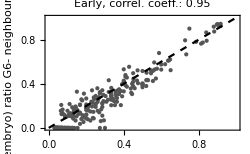
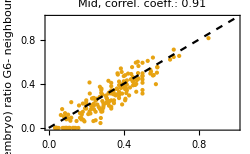
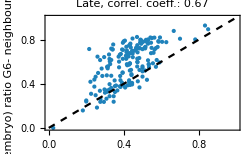

```mathematica
plotNeighbByStageG6m=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosG6SortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion G6- in ICM","mean (per embryo) ratio\nG6- neighbours of G6- cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageG6m[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageG6m.png"}],plotNeighbByStageG6m]
```

```mathematica
correlByStageG6p=Table [N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosG6SortedByStage[[i]],"MeanRatioPosNeighbPosCell"/.plotRatiosG6SortedByStage[[i]]],{i,1,3}]
```

{0.974591,0.955935,0.668932}

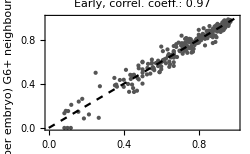
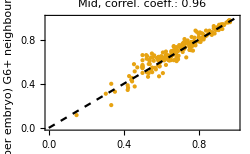
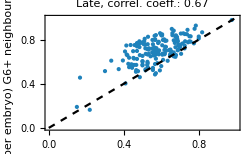

```mathematica
plotNeighbByStageG6p=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosG6SortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion G6+ in ICM","mean ratio (per embryo)\nG6+ neighbours of G6+ cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageG6p[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageG6p.png"}],plotNeighbByStageG6p]
```

#### By experiment

```mathematica
plotRatiosG6SortedRawByExp=SortBy[#,"CellNumberICM"/.#&]&/@{Join[plotRatiosG6SortedSMD2021,plotRatiosG6SortedJLG2021],plotRatiosG6SortedSMD2020,plotRatiosG6SortedNS2016,plotRatiosG6SortedNS2020RatGt,plotRatiosG6SortedNS2020RatRb,plotRatiosG6SortedNS2020};
```

```mathematica
plotRatiosG6SortedByExp=Table[Select[plotRatiosG6SortedRawByExp[[i]],NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&&("Stage"/.#)>3.&],{i,1,Length[plotRatiosG6SortedRawByExp]}];
```

```mathematica
plotRatiosG6SortedByExpByStage=Table[Table[Select[plotRatiosG6SortedByExp[[j]],("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}],{j,1,Length[plotRatiosG6SortedByExp]}];
```

```mathematica
plotRatiosG6SortedByExpByStage//Length
```

6

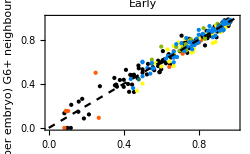
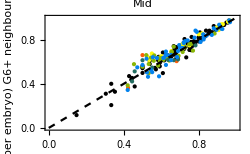
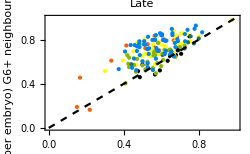

```mathematica
plotNeighbByExpByStageG6p=Row[Table[Show[Graphics[Table[{ColorData[3][j],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosG6SortedByExpByStage[[j,i]],{j,1,Length[plotRatiosG6SortedByExpByStage]}],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion G6+ in ICM","mean ratio (per embryo)\nG6+ neighbours of G6+ cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early","Mid","Late"}[[i]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByExpByStageG6p.png"}],plotNeighbByExpByStageG6p]
```

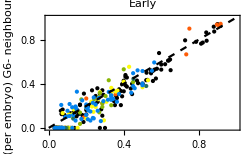
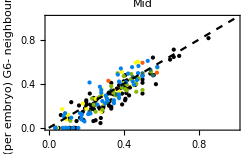
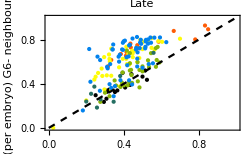

```mathematica
plotNeighbByExpByStageG6m=Row[Table[Show[Graphics[Table[{ColorData[3][j],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosG6SortedByExpByStage[[j,i]],{j,1,Length[plotRatiosG6SortedByExpByStage]}],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->250,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion G6- in ICM","mean ratio (per embryo)\nG6- neighbours of G6- cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early","Mid","Late"}[[i]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByExpByStageG6m.png"}],plotNeighbByExpByStageG6m]
```

```mathematica
neighbByExpLegend=SwatchLegend[ColorData[3]/@Range[Length[plotRatiosG6SortedByExpByStage]],{"Data Set I","Data set II","Data Set III","Data set IV","Data set V","Data set VI"},LegendLayout->"Row"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByExpLegend.png"}],neighbByExpLegend]
```